1	0.769204

2	0.828452

3	0.828355

4	0.828206

5	0.828155

6	0.828136

7	0.828127

8	0.828123

9	0.82812

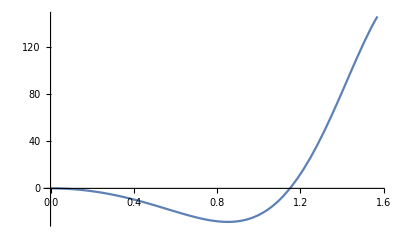

```mathematica
f[x_]:=Sin[x^2];
a=0;
b=Pi/2;
m4=D[f[x],{x,4}]/.x->Pi/2;
delta=10^(-4);
k0=50;
p[k_]:=(b-a)/(6k)*
(f[a]+f[b]+2Sum[f[a+i*(b-a)/(2k)],{i,2,2k-2,2}]+4Sum[f[a+i*(b-a)/(2k)],{i,1,2k-1,2}]);
Do[Print[k,"\t",N[p[k]]];
If[(b-a)^5/(180*(2k)^4)*m4<delta,Break[],If[k==k0,Print["fail to achieve the accuracy"]]],{k,k0}]
```